# Rubrik (skriv projektets namn här)

## MA2047/MA2051 Algebra och diskret matematik HT25

Rapportversion 1, inlämnad 2025 - mm - dd

## Grupp

Förnamn1 Efternamn1

Förnamn2 Efternamn2

Förnamn3 Efternamn3

Förnamn4 Efternamn4

## Uppgifter

### Instruktioner

Varje deluppgift i projektet ska redovisas enligt nedan.

Handledningar till Mathematica hittar du här: https://hh-mh.github.io/links.html

Svensk rättstavning kan väljas i 
Format->Option inspector->Formatting options->Text content options
eller genom att köra:

```mathematica
CurrentValue[EvaluationNotebook[],DefaultNaturalLanguage]="Swedish";
```

OBS! Rapporten måste klara “Ctrl-A + shift-return” utan att lämna något felmeddelande!

### 1)

#### Problem

Förklaring av problemet.  Vad ska göras? Ev referenser ska anges med nummer inom hakparenteser (se nedan).
Exempel: 
Vi ska här beräkna 572^29 mod 713 med hjälp av kvadreringsmetoden som visas i projektbeskrivningen[1].

#### Lösning

Redogörelse/lösningsförklaring och beräkningar med ev hänvisningar till nedanstående Mathematicakod.

Ev referenser anges också (se nedan).

Matematiska uttryck ska formateras korrekt. I en text används “Ctrl + (“ för start av det matematiska uttrycket och “Ctrl + )” för slut (motsvarar dollartecknet $ i LATEX). 
Exempel:
Med hjälp av  pq-formeln löser vi enkelt andragradsekvationen: x^2-2x=2⇔x_1=1+√3 eller x_2=1-√3.  Eftersom vi i det här fallet är ute efter den positiva roten är svaret på frågan 1+√3.

#### Mathematicakod

Utnyttjas Mathematica för beräkningar ska körbar kod visas här.

Grafen till TraditionalForm`f(x):

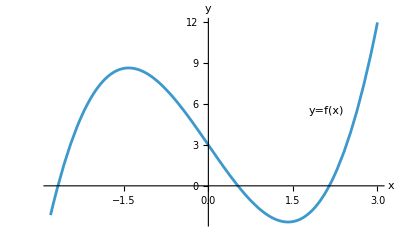

Derivatan: f'(x) = -6+3 x^2

Nollställena till f'(x): x1 = -√2 och x2 = √2.

Motsvarande funktionsvärden: f(x1) = 3+4 √2 och f(x2) = 3-4 √2

```mathematica
Remove["Global`*"]
f[x_]:=x^3-6x+3;
Print["Grafen till TraditionalForm`f(x):"]
Plot[f[x],{x,-2.8,3},AxesLabel->{x,y},Epilog->{Text["y=f(x)",{2.1,5.5}]}]
(* Nollställena till f'(x) *)
nollst=Solve[f'[x]==0,x];
x1=nollst[[1,1,2]];
x2=nollst[[2,1,2]];
Print["Derivatan: f'(x) = ",f'[x]];Print["Nollställena till f'(x): x1 = ",x1," och " ,"x2 = ",x2,"."]
Print["Motsvarande funktionsvärden: f(x1) = ",f[x1]," och ","f(x2) = ",f[x2]]
```

#### Slutsatser och resultat

Vad blir resultatet/svaret? Är resultatet rimligt? Vilka slutsatser kan dras av ovanstående beräkningar?

## Referenser

Här anges vilka källor som utnyttjats och som refereras till i rapporten. 
Exempel:

[1] Projektuppgift 1.5 hp,  https://hh-mh.github.io/teaching/algdisk/project.html

[2] J. Johansson och S. Lemurell, Algebra och diskret matematik, Studentlitteratur (2013)

[3] Wikipedia, RSA Numbers, http://en.wikipedia.org/wiki/RSA_numbers